#### Rule

Add[9,b]

#### 在递归问题中加速计算的方法

```mathematica
f[1]=1;
f[2]=1;
(*fn直接延迟赋值会使某些函数计算会重复很多次，写成下面这样就会提高效率*)
f[n_]:=f[n]=f[n-1]+f[n-2];
```

```mathematica
f[40]
```

102334155

#### 系数为正负1的全体n次幂方程的根的复平面图形

```mathematica
(*例如n=2时的1+x+x^2==0，需要列出所有可能*)
(*方程和n的关系是in^0+jn^1,kn^2,ln^3....xn^n*)
(*系数生成*)
Tuples[{1,-1},3]
```

{{1,1,1},{1,1,-1},{1,-1,1},{1,-1,-1},{-1,1,1},{-1,1,-1},{-1,-1,1},{-1,-1,-1}}

```mathematica
(*多项式生成*)
```

```mathematica
x^Range[0,2]
```

{1,x,x^2}

```mathematica
(*生成方程的函数*)
```

```mathematica
EquationList[n_]:=Module[{},
((x^Range[0,n]).#&)/@Tuples[{1,-1},n+1]
];
EquationList[2]
```

{1+x+x^2,1+x-x^2,1-x+x^2,1-x-x^2,-1+x+x^2,-1+x-x^2,-1-x+x^2,-1-x-x^2}

```mathematica
(*解方程*)
```

```mathematica
NSolve[1+x+x^2,x]
```

{{x→-0.5-0.866025 ⅈ},{x→-0.5+0.866025 ⅈ}}

```mathematica
(*提取实部和虚部作为坐标*)
```

```mathematica
x/.{{x->-0.5-0.8660254037844386 ⅈ},{x->-0.5+0.8660254037844386 ⅈ}}//ReIm
```

{{-0.5,-0.866025},{-0.5,0.866025}}

```mathematica
(*最终结果*)
```

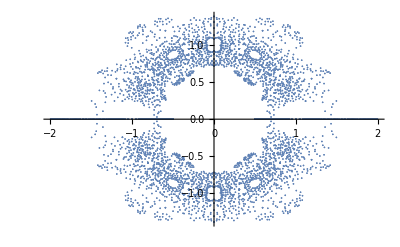

```mathematica
x/.NSolve[#,x]&/@EquationList[9]//Flatten//ReIm//ListPlot
```

#### 更有效率的做法:用NRoots

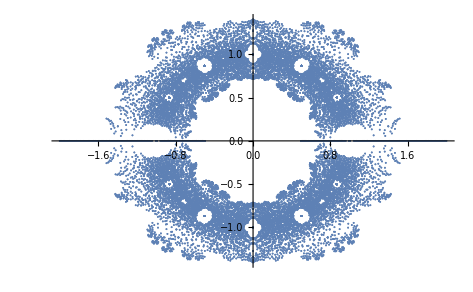

```mathematica
List@@#&/@(NRoots[#,x]&/@EquationList[11])[[All,All,2]]//Flatten//ReIm//ListPlot
```